```mathematica
y=2009;
```

```mathematica
dowJonesMember={"MMM","AXP","AAPL","BA","CAT","CVX","CSCO","KO","DD","XOM","GE","GS","HD","INTC","IBM","JNJ","JPM","MCD","MRK","MSFT","NKE","PFE","PG","TRV","UNH","UTX","VZ","WMT","DIS"};
```

```mathematica
stocksSets=splitup[dowJonesMember,5];
Length/@stocksSets
```

{5,6,6,6,6}

```mathematica
trainingSets=Flatten[Drop[stocksSets,{#}]]&/@Range[Length[stocksSets]];
testSets=stocksSets[[#]]&/@Range[Length[stocksSets]];
```

```mathematica
trainingSet=x[2005,2012]/@dowJonesMember;
```

```mathematica
trainingSets=splitup[trainingSet,5];
```

```mathematica
trainingSets=Function[n,
Flatten[Drop[trainingSets,{n}],2]]/@Range[Length[trainingSets]];
```

```mathematica
Dimensions/@trainingSets
```

{{42288,64},{40526,64},{40526,64},{40526,64},{40526,64}}

```mathematica
{Φs,As,bs}=Transpose[Φ/@trainingSets];
```

```mathematica
trainingReturns=r[2005,2012]/@dowJonesMember;
```

```mathematica
trainingReturns=splitup[testReturns,5];
```

```mathematica
trainingReturns=Function[n,
Flatten[Drop[trainingReturns,{n}]]]/@Range[Length[trainingReturns]];
```

```mathematica
Dimensions/@trainingReturns
```

{{42288},{40526},{40526},{40526},{40526}}

```mathematica
qs=MapThread[findQ[0,1,#1,#2]&,{Φs,trainingReturns}];
```

```mathematica
Norm/@qs
```

{1.,1.,1.,1.,1.}

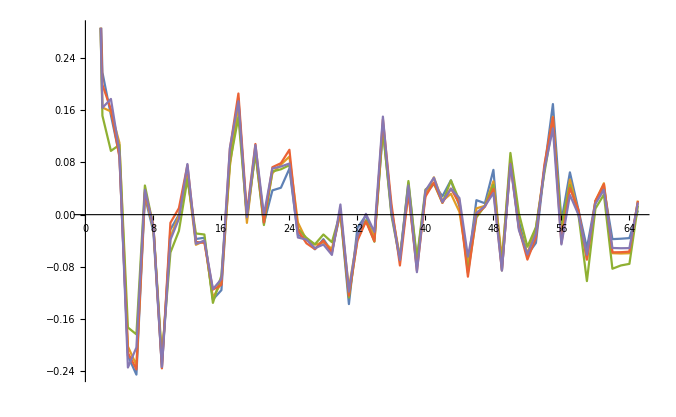

```mathematica
ListLinePlot[qs]
```